```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\triplet_nucleation\R33R11\b3small\zigcenter\scan

```mathematica
PotenData=Import["P1_scan.txt","Data"]
```

{{-171.981,-1306.52},{-161.981,-1306.52},{-151.981,-1306.54},{-141.981,-1306.55},{-131.981,-1306.55},{-121.981,-1306.55},{-111.981,-1306.55},{-101.981,-1306.55},{-91.981,-1306.55},{-90.019,-1306.55},{-80.019,-1306.55},{-70.019,-1306.55},{-60.019,-1306.55},{-50.019,-1306.55},{-40.019,-1306.55},{-30.019,-1306.54},{-20.019,-1306.54},{-10.019,-1306.53},{-0.0189523,-1306.52},{9.98105,-1306.51},{19.981,-1306.54},{29.981,-1306.54},{39.981,-1306.55},{49.981,-1306.55},{59.981,-1306.55},{69.981,-1306.55},{79.981,-1306.55},{89.981,-1306.55},{99.981,-1306.55},{109.981,-1306.55},{119.981,-1306.55},{129.981,-1306.55},{139.981,-1306.55},{149.981,-1306.54},{159.981,-1306.54},{169.981,-1306.53},{179.981,-1306.52}}

```mathematica
Dih=PotenData⟦All,1⟧
```

{-171.981,-161.981,-151.981,-141.981,-131.981,-121.981,-111.981,-101.981,-91.981,-90.019,-80.019,-70.019,-60.019,-50.019,-40.019,-30.019,-20.019,-10.019,-0.0189523,9.98105,19.981,29.981,39.981,49.981,59.981,69.981,79.981,89.981,99.981,109.981,119.981,129.981,139.981,149.981,159.981,169.981,179.981}

```mathematica
DihRad=Dih/360*2*3.14
```

{-3.00011,-2.82567,-2.65122,-2.47678,-2.30234,-2.12789,-1.95345,-1.779,-1.60456,-1.57033,-1.39589,-1.22144,-1.047,-0.872553,-0.698108,-0.523664,-0.34922,-0.174775,-0.000330613,0.174114,0.348558,0.523003,0.697447,0.871892,1.04634,1.22078,1.39522,1.56967,1.74411,1.91856,2.093,2.26745,2.44189,2.61634,2.79078,2.96522,3.13967}

```mathematica
Pot=PotenData⟦All,2⟧
```

{-1306.52,-1306.52,-1306.54,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.54,-1306.54,-1306.53,-1306.52,-1306.51,-1306.54,-1306.54,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.55,-1306.54,-1306.54,-1306.53,-1306.52}

```mathematica
Potkcal=(Pot-Min[Pot])*627.51
```

{18.4041,18.0743,6.32071,3.41801,1.57356,0.558998,0.125521,0.0287964,0.,6.27503×10^-6,0.0286835,0.125577,0.563636,1.59808,3.42925,6.2677,10.1143,14.9741,20.7928,27.3954,10.1308,6.28041,3.43805,1.60336,0.566284,0.126399,0.028809,6.27503×10^-6,0.0286647,0.124711,0.556419,1.56834,3.40909,6.30751,10.456,15.9281,22.6507}

```mathematica
PotDataRad=Table[{DihRad⟦i⟧,Pot⟦i⟧},{i,1,Length[Pot]}]
```

{{-3.00011,-1306.52},{-2.82567,-1306.52},{-2.65122,-1306.54},{-2.47678,-1306.55},{-2.30234,-1306.55},{-2.12789,-1306.55},{-1.95345,-1306.55},{-1.779,-1306.55},{-1.60456,-1306.55},{-1.57033,-1306.55},{-1.39589,-1306.55},{-1.22144,-1306.55},{-1.047,-1306.55},{-0.872553,-1306.55},{-0.698108,-1306.55},{-0.523664,-1306.54},{-0.34922,-1306.54},{-0.174775,-1306.53},{-0.000330613,-1306.52},{0.174114,-1306.51},{0.348558,-1306.54},{0.523003,-1306.54},{0.697447,-1306.55},{0.871892,-1306.55},{1.04634,-1306.55},{1.22078,-1306.55},{1.39522,-1306.55},{1.56967,-1306.55},{1.74411,-1306.55},{1.91856,-1306.55},{2.093,-1306.55},{2.26745,-1306.55},{2.44189,-1306.55},{2.61634,-1306.54},{2.79078,-1306.54},{2.96522,-1306.53},{3.13967,-1306.52}}

```mathematica
PotkcalDataRad=Table[{DihRad⟦i⟧,Potkcal⟦i⟧},{i,1,Length[Pot]}]
```

{{-3.00011,18.4041},{-2.82567,18.0743},{-2.65122,6.32071},{-2.47678,3.41801},{-2.30234,1.57356},{-2.12789,0.558998},{-1.95345,0.125521},{-1.779,0.0287964},{-1.60456,0.},{-1.57033,6.27503×10^-6},{-1.39589,0.0286835},{-1.22144,0.125577},{-1.047,0.563636},{-0.872553,1.59808},{-0.698108,3.42925},{-0.523664,6.2677},{-0.34922,10.1143},{-0.174775,14.9741},{-0.000330613,20.7928},{0.174114,27.3954},{0.348558,10.1308},{0.523003,6.28041},{0.697447,3.43805},{0.871892,1.60336},{1.04634,0.566284},{1.22078,0.126399},{1.39522,0.028809},{1.56967,6.27503×10^-6},{1.74411,0.0286647},{1.91856,0.124711},{2.093,0.556419},{2.26745,1.56834},{2.44189,3.40909},{2.61634,6.30751},{2.79078,10.456},{2.96522,15.9281},{3.13967,22.6507}}

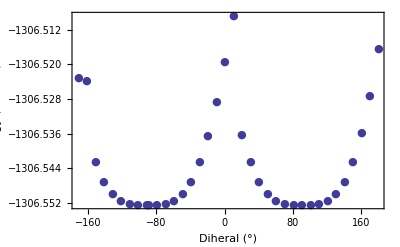

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (°)",Italic,17],}};
ListPlot[PotenData,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium}
                    ]
```

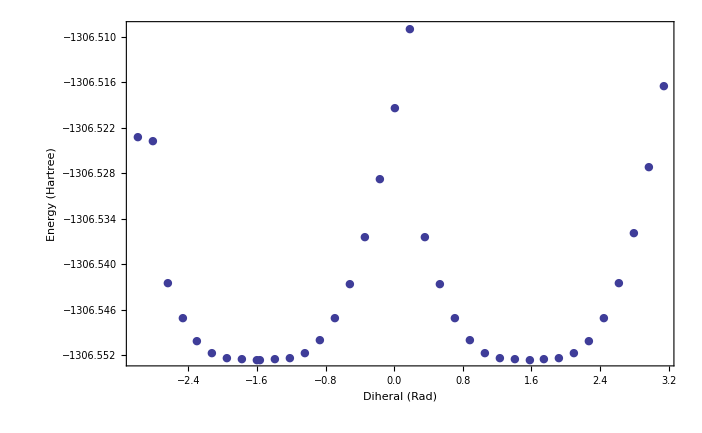

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
datainterrot=ListPlot[PotDataRad,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium}
                    ]
```

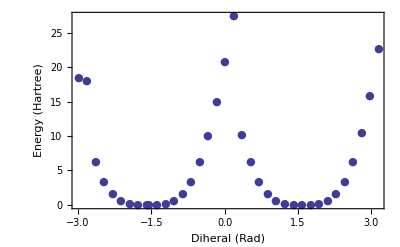

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
datainterrotkcal=ListPlot[PotkcalDataRad,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium}
                    ]
```

```mathematica
PotDataRadInt=Interpolation[PotDataRad]
```

InterpolatingFunction[{{-3.00011,3.13967}},<>]

```mathematica
PotkcalDataRadInt=Interpolation[PotkcalDataRad]
```

InterpolatingFunction[{{-3.00011,3.13967}},<>]

InterpolatingFunction::dmval: Input value {-3.1414642970899465`} lies outside the range of data in the interpolating function. Extrapolation will be used.

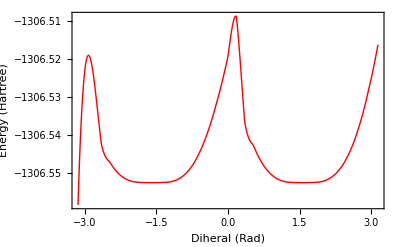

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
figure=Plot[PotDataRadInt[x],{x,-π,π},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ]
```

InterpolatingFunction::dmval: Input value {-3.1414642970899465`} lies outside the range of data in the interpolating function. Extrapolation will be used.

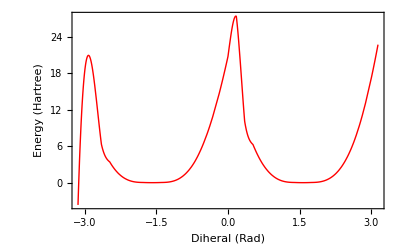

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
figure=Plot[PotkcalDataRadInt[x],{x,-π,π},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,PlotStyle-> Red,AxesStyle-> White
                    ]
```

### Fourier

#### Hartree

```mathematica
plotfun[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotDataRadInt[x],{x,-π,π}];
a[n_]:=1/π NIntegrate[PotDataRadInt[x]*Cos[n*x],{x,-π,π}];
b[n_]:=1/π NIntegrate[PotDataRadInt[x]*Sin[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[a[i]*Cos[i*y],{i,serieslength}]+Sum[b[i]*Sin[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plotfuncos[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotDataRadInt[x],{x,-π,π}];
a[n_]:=1/π NIntegrate[PotDataRadInt[x]*Cos[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[a[i]*Cos[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plotfunsin[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotDataRadInt[x],{x,-π,π}];
b[n_]:=1/π NIntegrate[PotDataRadInt[x]*Sin[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[b[i]*Sin[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plot2=plotfun[2]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]}

```mathematica
plot3=plotfun[3]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]}

```mathematica
plot4=plotfun[4]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]}

```mathematica
plot5=plotfun[5]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]}

```mathematica
plot6=plotfun[6]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]+0.00153858 Sin[6 x]}

```mathematica
plot7=plotfun[7]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]+0.00153858 Sin[6 x]+0.000488814 Sin[7 x]}

```mathematica
plot8=plotfun[8]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]+0.00153858 Sin[6 x]+0.000488814 Sin[7 x]+0.00137556 Sin[8 x]}

```mathematica
plot9=plotfun[9]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]+0.00123447 Cos[9 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]+0.00153858 Sin[6 x]+0.000488814 Sin[7 x]+0.00137556 Sin[8 x]+0.000875783 Sin[9 x]}

```mathematica
plot10=plotfun[10]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]+0.00123447 Cos[9 x]-0.000603621 Cos[10 x]+0.0000860277 Sin[x]+0.000609928 Sin[2 x]+0.000155375 Sin[3 x]+0.00123407 Sin[4 x]+0.00021863 Sin[5 x]+0.00153858 Sin[6 x]+0.000488814 Sin[7 x]+0.00137556 Sin[8 x]+0.000875783 Sin[9 x]+0.000884222 Sin[10 x]}

```mathematica
plotcos4=plotfuncos[4]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]}

```mathematica
plotcos6=plotfuncos[6]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]}

```mathematica
FortranForm[plotcos6]
```

List(-1306.543432364388 + 0.0008534442643617455*Cos(x) + 0.013713134211520771*Cos(2*x) + 0.0008566582851139432*Cos(3*x) + 0.0062273307245474235*Cos(4*x) + 
     -   0.0010530453510189082*Cos(5*x) + 0.0020844669360625865*Cos(6*x))

```mathematica
plotcos8=plotfuncos[8]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]}

```mathematica
plotcos20=plotfuncos[20]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]+0.00123447 Cos[9 x]-0.000603621 Cos[10 x]+0.000941949 Cos[11 x]-0.00101395 Cos[12 x]+0.000506895 Cos[13 x]-0.00101369 Cos[14 x]+0.000110568 Cos[15 x]-0.000829388 Cos[16 x]-0.0000950823 Cos[17 x]-0.000600438 Cos[18 x]-0.0000872143 Cos[19 x]-0.000433138 Cos[20 x]}

```mathematica
plotcos10=plotfuncos[10]
```

{-1306.54+0.000853444 Cos[x]+0.0137131 Cos[2 x]+0.000856658 Cos[3 x]+0.00622733 Cos[4 x]+0.00105305 Cos[5 x]+0.00208447 Cos[6 x]+0.00126423 Cos[7 x]+0.000369218 Cos[8 x]+0.00123447 Cos[9 x]-0.000603621 Cos[10 x]}

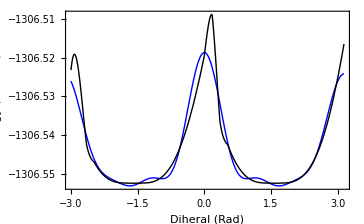

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[{plotcos6,PotDataRadInt[x]},{x,DihRad⟦1⟧,DihRad⟦Length[DihRad]⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},PlotStyle->{Blue,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

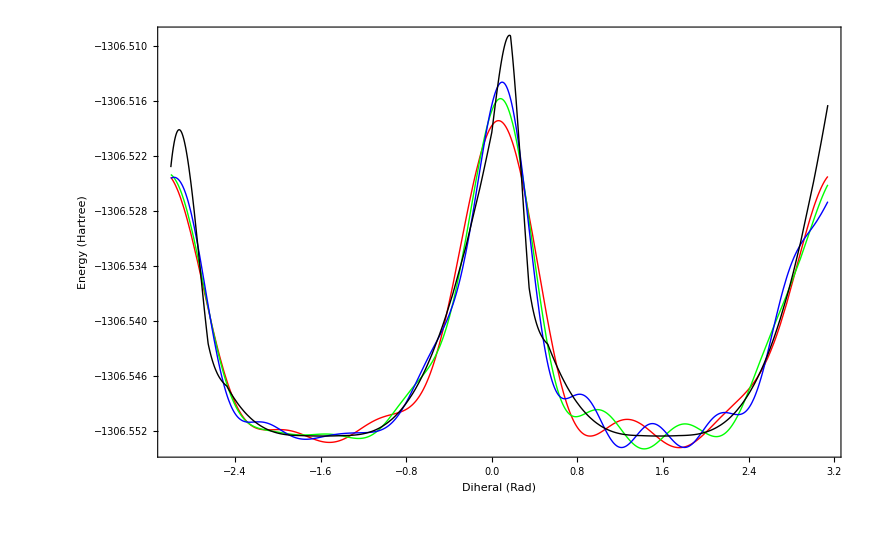

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[{plot6,plot8,plot10,PotDataRadInt[x]},{x,DihRad⟦1⟧,DihRad⟦Length[DihRad]⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},PlotStyle->{Red,Green,Blue,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

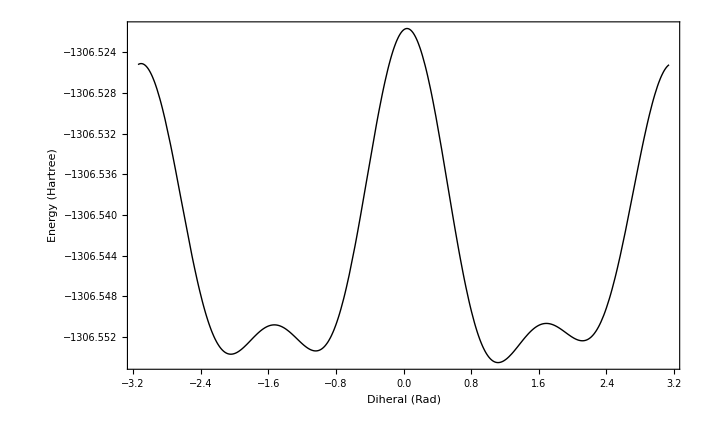

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
fitinterrot=Plot[plot4,{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},PlotStyle->{Red,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

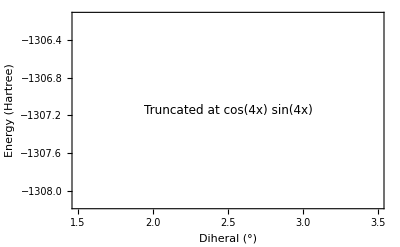

```mathematica
formular="Truncated at cos(4x) sin(4x)";
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (°)",Italic,17],}};
formplot=Graphics[{Text[Style[formular,{12,Italic}],{2.5,-1307.14777332}]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
                  ]
```

```mathematica
IM3=Show[datainterrot,fitinterrot,formplot]
```

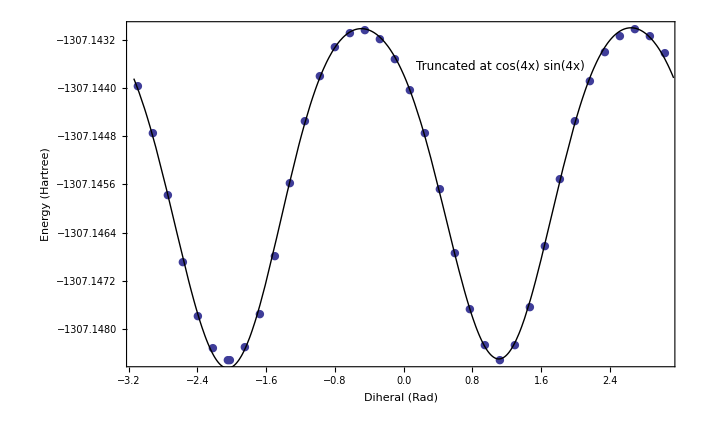

```mathematica
IM1=Show[datainterrot,fitinterrot,formplot]
```

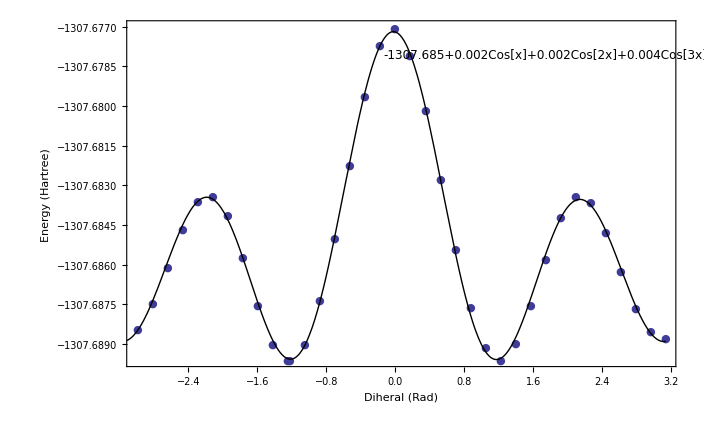

```mathematica
IM2=Show[datainterrot,fitinterrot,formplot]
```

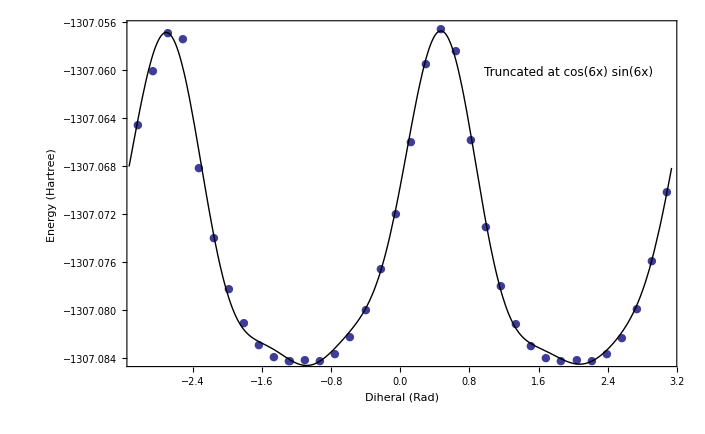

#### kcal/mol

```mathematica
plotfunkcal[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotkcalDataRadInt[x],{x,-π,π}];
a[n_]:=1/π NIntegrate[PotkcalDataRadInt[x]*Cos[n*x],{x,-π,π}];
b[n_]:=1/π NIntegrate[PotkcalDataRadInt[x]*Sin[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[a[i]*Cos[i*y],{i,serieslength}]+Sum[b[i]*Sin[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plotfunkcalcos[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotkcalDataRadInt[x],{x,-π,π}];
a[n_]:=1/π NIntegrate[PotkcalDataRadInt[x]*Cos[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[a[i]*Cos[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plotfunkcalsin[num_]:={serieslength=num;
a0=1/(2*π)NIntegrate[PotkcalDataRadInt[x],{x,-π,π}];
b[n_]:=1/π NIntegrate[PotkcalDataRadInt[x]*Sin[n*x],{x,-π,π}];
FitFunction[y_]:=a0+Sum[b[i]*Sin[i*y],{i,serieslength}];
FitFunction[x]}
```

```mathematica
plotkcalcos6=plotfunkcalcos[6]
```

{5.69586+0.535545 Cos[x]+8.60513 Cos[2 x]+0.537562 Cos[3 x]+3.90771 Cos[4 x]+0.660796 Cos[5 x]+1.30802 Cos[6 x]}

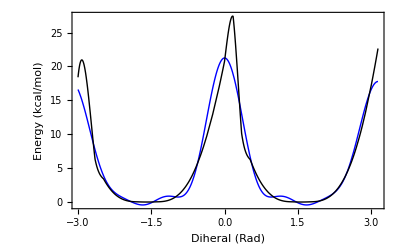

```mathematica
plotframedGT={{Style["Energy (kcal/mol)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[{plotkcalcos6,PotkcalDataRadInt[x]},{x,DihRad⟦1⟧,DihRad⟦Length[DihRad]⟧},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},PlotStyle->{Blue,Black}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

#### debug

```mathematica
serieslength=2
```

3

```mathematica
a0=1/(2*π)NIntegrate[PotDataRadInt[x],{x,-π,π}]
```

0.118433

```mathematica
a[n_]:=1/π NIntegrate[PotDataRadInt[x]*Cos[n*x],{x,-π,π}]
```

```mathematica
Table[a[n],{n,1,serieslength}]
```

{0.00183253,0.00231216,0.00190969}

```mathematica
b[n_]:=1/π NIntegrate[PotDataRadInt[x]*Sin[n*x],{x,-π,π}]
```

```mathematica
Table[b[n],{n,1,serieslength}]
```

{-4.62434×10^-8,4.40577×10^-8,-1.16595×10^-8}

```mathematica
FitFunction[x_]:=a0+Sum[a[i]*Cos[i*x],{i,serieslength}]+Sum[b[i]*Sin[i*x],{i,serieslength}]
```

```mathematica
plotfun=FitFunction[x]
```

0.118433+0.00183253 Cos[x]+0.00231216 Cos[2 x]+0.00190969 Cos[3 x]-4.62434×10^-8 Sin[x]+4.40577×10^-8 Sin[2 x]-1.16595×10^-8 Sin[3 x]

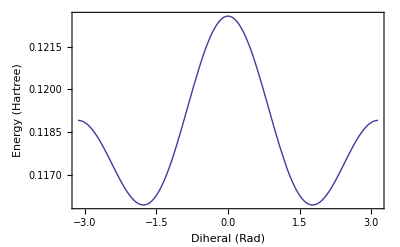

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
trun2=Plot[plotfun,{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

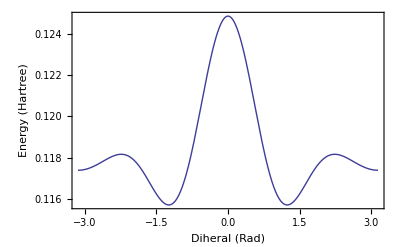

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
trun4=Plot[plotfun,{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

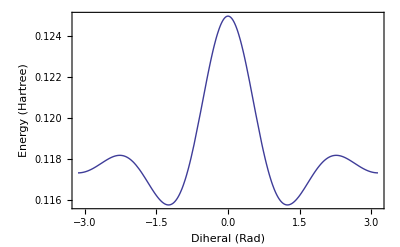

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
trun6=Plot[plotfun,{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

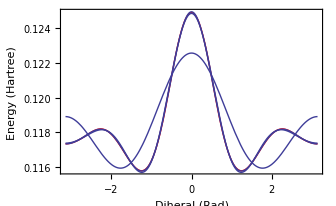

```mathematica
Show[{figure,trun2,trun4,trun6}]
```

### Fail

```mathematica
Fourier[Pot]
```

{0.720225+0. ⅈ,-0.00541945+0.000463084 ⅈ,0.00664491-0.00114345 ⅈ,-0.00580449+0.00151711 ⅈ,0.00137499-0.000487713 ⅈ,-0.000178659+0.0000810633 ⅈ,0.00010596-0.000059413 ⅈ,0.00004914-0.0000333614 ⅈ,-0.0000202262+0.0000164189 ⅈ,0.000023327-0.0000225195 ⅈ,-0.0000138125+0.0000156714 ⅈ,6.24972×10^-6-8.61521×10^-6 ⅈ,-6.84033×10^-7+1.01405×10^-6 ⅈ,1.36173×10^-6-2.61065×10^-6 ⅈ,1.67148×10^-6-4.06376×10^-6 ⅈ,1.22237×10^-7-4.10018×10^-7 ⅈ,6.23002×10^-7-3.07607×10^-6 ⅈ,-5.43736×10^-8+1.48031×10^-7 ⅈ,6.18035×10^-8-1.17413×10^-6 ⅈ,6.18035×10^-8+1.17413×10^-6 ⅈ,-5.43736×10^-8-1.48031×10^-7 ⅈ,6.23002×10^-7+3.07607×10^-6 ⅈ,1.22237×10^-7+4.10018×10^-7 ⅈ,1.67148×10^-6+4.06376×10^-6 ⅈ,1.36173×10^-6+2.61065×10^-6 ⅈ,-6.84033×10^-7-1.01405×10^-6 ⅈ,6.24972×10^-6+8.61521×10^-6 ⅈ,-0.0000138125-0.0000156714 ⅈ,0.000023327+0.0000225195 ⅈ,-0.0000202262-0.0000164189 ⅈ,0.00004914+0.0000333614 ⅈ,0.00010596+0.000059413 ⅈ,-0.000178659-0.0000810633 ⅈ,0.00137499+0.000487713 ⅈ,-0.00580449-0.00151711 ⅈ,0.00664491+0.00114345 ⅈ,-0.00541945-0.000463084 ⅈ}

```mathematica
CosFourierCoe=Re[Fourier[Pot]]*2*3.14/Length[Pot]
```

{0.122244,-0.000919842,0.00112784,-0.000985194,0.000233376,-0.0000303237,0.0000179845,8.34052×10^-6,-3.43299×10^-6,3.95929×10^-6,-2.34439×10^-6,1.06076×10^-6,-1.16101×10^-7,2.31126×10^-7,2.83699×10^-7,2.07473×10^-8,1.05742×10^-7,-9.22882×10^-9,1.04899×10^-8,1.04899×10^-8,-9.22882×10^-9,1.05742×10^-7,2.07473×10^-8,2.83699×10^-7,2.31126×10^-7,-1.16101×10^-7,1.06076×10^-6,-2.34439×10^-6,3.95929×10^-6,-3.43299×10^-6,8.34052×10^-6,0.0000179845,-0.0000303237,0.000233376,-0.000985194,0.00112784,-0.000919842}

```mathematica
FitFunction[x_]:=Sum[CosFourierCoe⟦i⟧*Cos[(i-1)*x],{i,1,Length[Pot]}]
```

```mathematica
FitFunction[0]
```

0.121148

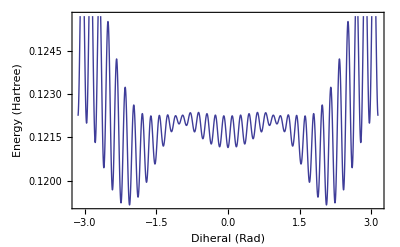

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[FitFunction[x],{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```

```mathematica
FourierTrigSeries[PotDataRadInt[x],x,10]
```

FourierTrigSeries[InterpolatingFunction[{{-3.13968,3.14032}},<>][x],x,10]

```mathematica
CosFourierCoe=FourierDCT[Pot]*2*3.14/Length[Pot]
```

{0.122244,1.85351×10^-7,-0.000923194,-4.4292×10^-7,0.00114442,9.22239×10^-7,-0.00101829,-6.70275×10^-7,0.000247622,8.34982×10^-8,-0.0000332991,-6.164×10^-8,0.0000206187,-1.16379×10^-8,0.000010081,8.74814×10^-9,-4.42169×10^-6,-2.41385×10^-8,5.50318×10^-6,2.29602×10^-9,-3.54559×10^-6,-9.59176×10^-9,1.80641×10^-6,6.37143×10^-9,-2.07433×10^-7,1.29441×10^-8,4.99713×10^-7,1.07836×10^-9,7.45783×10^-7,-6.12561×10^-9,7.2617×10^-8,-6.24261×10^-9,5.3266×10^-7,-9.77657×10^-11,-2.6094×10^-8,5.47838×10^-9,1.9955×10^-7}

```mathematica
FitFunction[x_]:=Sum[CosFourierCoe⟦i⟧*Cos[(i-1)*x],{i,1,Length[Pot]}]
```

```mathematica
FitFunction[0]
```

0.121693

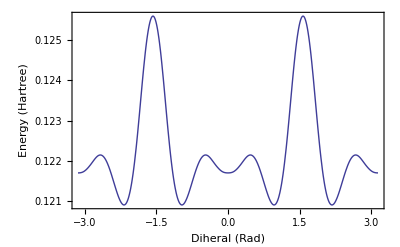

```mathematica
plotframedGT={{Style["Energy (Hartree)",Italic,17],},{Style[" Diheral (Rad)",Italic,17],}};
Plot[FitFunction[x],{x,-3.14,3.14},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed}
               (*   PlotMarkers-> {Automatic,Medium*)
                    ]
```